# Mathematica与数学建模 自动化1402 徐国栋

```mathematica
Why Mathematica
```

非常非常简单..即使你不懂编程.

### 求不定积分

```mathematica
∫1/(1-x^3)ⅆx
```

ArcTan[(1+2 x)/(√3)]/(√3)-1/3 Log[1-x]+1/6 Log[1+x+x^2]

### 画图

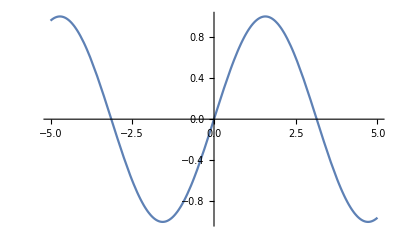

```mathematica
Plot[Sin[x],{x,-5,5}]
```

### 自然语言

#### 如果我们想画一个绿色的圈?

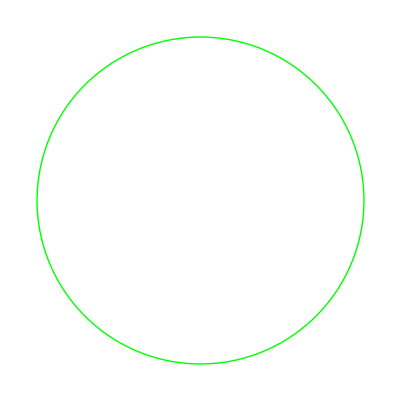

```mathematica
LinguisticAssistant
```

#### 如果我们想求出前500个质数的和, 又不想编程?

```mathematica
LinguisticAssistant
```

824693

交互式的环境

```mathematica
Manipulate[Plot[am*func[w*x],{x,-5,5}],{w,1,5},{am,1,5},{func,{Sin,Cos,Tan,ArcTan,ArcSin}}]
```

```mathematica
一个例子: 摆线



即一个圆在平面上滚动时, 其上一个点形成的轨迹. 我们很难自己想象出这样一个轨迹的形状. 


 利用其交互性的功能, 我们很容易可以仿真出这条轨迹.
```

## 摆线

```mathematica
d=5;R=3;
Animate[ParametricPlot[{R t-d Sin[t],R-d Cos[t]},{t,-Pi,t},PlotStyle->{Thick,Blue}],{t,-Pi+0.01,4Pi}]
```

```mathematica
Animate[Show[ParametricPlot[{R t-d Sin[t],R-d Cos[t]},{t,-Pi,t},PlotStyle->{Thick,Blue}],Graphics[{{Circle[{R t,R},R]},{Thick,Line[{{R t,R},{R t-d Sin[t],R-d Cos[t]}}]},{Line[{{-R Pi,0},{3 R Pi,0}}]},{Red,Disk[{R t-d Sin[t],R-d Cos[t]},0.1*R]}}],PlotRange->{{-R Pi,3 R Pi},{-d,R+d}},Axes->None],{t,-Pi+0.01,3 Pi}]
```

函数式编程

### 运算基于函数, 有函数式编程的很多好处. 如函数重载. 想学函数编程的同学可以看看SICP, 学学Scheme语言, 进一步可以尝试Haskell语言. 这是一个纯函数式的语言, 一些特性非常奇妙, 比如惰性求值, 高阶函数等, 这里不做介绍. -Graphics-

## 元胞自动机-Conway 生命游戏

```mathematica
在一个有边界的二维网格(Grid)中，每个格子中生活着一个细胞(Cell)；每个细胞只有两种生命状态：生(Alive)或死(Dead)；网格矩阵边界之外没有细胞；

每天天一亮，所有格子里的细胞都统一通过下面4个规则，进化到下一代。每个细胞下一代的生命状态与自己和8个邻居进化前的生命状态有关：

1）对于活的细胞，若其活着的邻居过于稀少，以至于少于2个，那么它的下一代就死去了；
2）对于活的细胞，若其活着的邻居过于稠密，以至于多于3个，那么它的下一代也会死去；
3）对于活的细胞，若其活着的邻居恰好是2~3个，那么它的下一代会接着愉快地活着；
4）对于死的细胞，若其活着的邻居恰好是3个，那么它的下一代会复生。
```

## 元胞自动机

```mathematica
函数重载
```

```mathematica
6行代码
```

```mathematica
check=RandomInteger[1,{100,100}];
updata[1,2]:=1;
updata[_,3]:=1;
updata[_,_]:=0;
SetAttributes[updata,Listable]
Dynamic[ArrayPlot[check=updata[check,Plus@@Map[RotateRight[check,#]&,{{-1,-1},{-1,0},{-1,1},{0,1},{0,-1},{1,-1},{1,0},{1,1}}]]]]
```

强大的内置函数

### 基于函数式编程, 内置函数非常多, 并且功能非常完善.

```mathematica
Octave
```

## 分形

Julia集-复数域


f(z)=z^2+c 对一个复平面上的任一点, 用这个函数对其进行迭代, 可以形成一个迭代序列, {f(z), f(f(z)), f(f(f(z))), f(f(f(f(z)))), ...}, 这个序列的模的收敛性根据点的位置不同是不同的.

## 分形

也就是说对f(z)=z^2+c, 任何一个不同的C, 我们都可以确定出一个不同的Julia集.

实现上, 首先我们定义一个迭代函数, 给定一个复平面上的点 z = x + y * i 对其进行Julia集的迭代, 输出为其模逃逸出2的迭代次数, 输入为X,Y,C_x, C_y, 以及迭代序列的长度(因为我们没办法计算到无穷大).

```mathematica
julia[x_,y_,lim_,cx_,cy_]:=
 Block[{z,ct=0},z=x+I*y;
    While[(Abs[z]<2.0)&&(ct<lim),++ct;
  z=z*z+(cx+I*cy);];Return[ct];]
```

```mathematica
DensityPlot[julia[x,y,50,0.11,0.66],
                {x,-1.5,1.5},{y,-1.5,1.5},
                  PlotPoints->120, Mesh->False]
```

-Graphics-

## 分形

```mathematica
内置函数, 性能有专门的优化, 并且一些参数会为你自动选择, 不需要调参数, 我们前面的参数就是序列长度. 利用内置函数, 我们只需要提供C的值.
```

```mathematica
JuliaSetPlot[0.11+0.66I,PlotLegends->Automatic]
```

-Graphics-

```mathematica
MandelbrotSetPlot[{-0.65+0.47I,-0.4+0.72I},MaxIterations->200,ColorFunction->"RedBlueTones"]
```

-Graphics-

适合任何人, 不仅仅是数学建模

### 不管你是什么专业, 它都有相应的功能.

## 数学

### 一个例子 - 积分

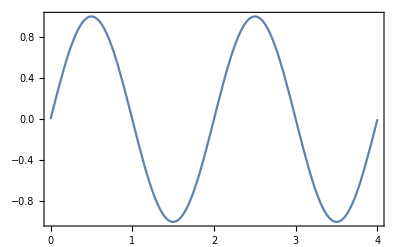

```mathematica
intEg1Plt1=Plot[Sin[π x],{x,0,4},AxesOrigin->{0,0},Frame->True]
```

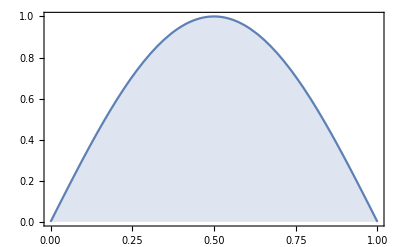

```mathematica
intEg1Plt2=Plot[Sin[π x],{x,0,1},AxesOrigin->{0,0},Filling->Axis,Frame->True]
```

```mathematica
LeftValue[f_,{x_,a_,b_}]:=N[f/.x->a];
MidpointValue[f_,{x_,a_,b_}]:=N[f/.x->(a+b)/2];
RightValue[f_,{x_,a_,b_}]:=N[f/.x->b];
Sample[f_,{x_,a_,b_},type_]:={LeftValue[f,{x,a,b}],MidpointValue[f,{x,a,b}],RightValue[f,{x,a,b}]}[[type]];
BlockCoords[a_,b_,h_]:={{a,0},{a,h},{b,h},{b,0}};
RiemannBlocks[f_,{x_,a_,b_,n_},type_]:=Plot[f,{x,a,b},Prolog->Table[({{GrayLevel[0.8],Polygon[#1]},Line[Append[#1,#1[[1]]]]}&)[(BlockCoords[#1,#2,Sample[f,{x,#1,#2},type]]&)[a+i*((b-a)/n),a+(i+1)*((b-a)/n)]],{i,0,n-1}],Frame->True]
```

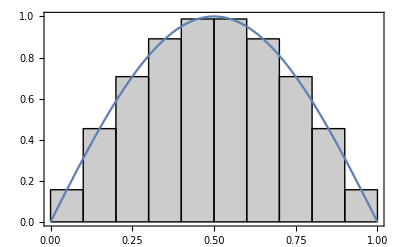

```mathematica
RiemannBlocks[Sin[π x],{x,0,1,10},2]
```

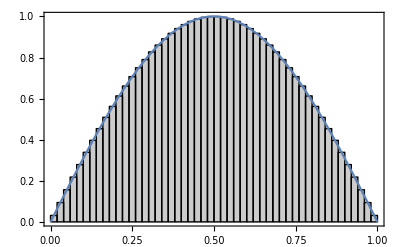

```mathematica
RiemannBlocks[Sin[π x],{x,0,1,50},2]
```

```mathematica
(∫_0)^1 f(x)dx
```

## 化学

```mathematica
毛地黄皂苷
```

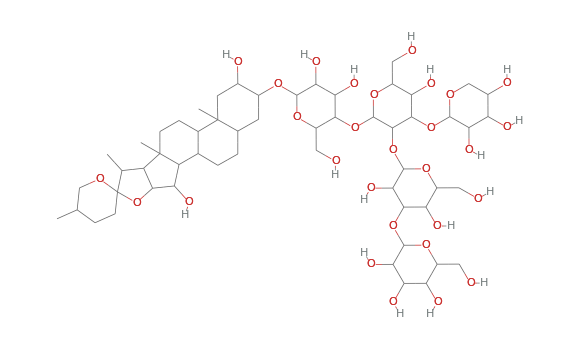

```mathematica
ChemicalData["Digitonin","ColorStructureDiagram"]
```

```mathematica
ChemicalData["Digitonin","MoleculePlot"]
```

-Graphics3D-

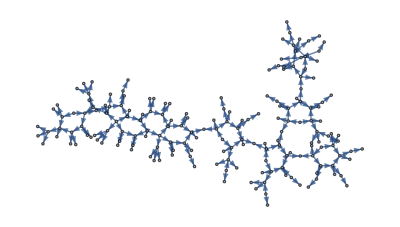

```mathematica
g=Graph[ChemicalData["Digitonin","EdgeRules"],GraphLayout->"SpringEmbedding"]
```

## 数学建模中的应用

数据类型题目 - 拟合

数据类型题目 - 插值

数据类型题目 - 预测问题

微分方程

优化问题

图论

数据类型题目 - 拟合

#### 2011数学建模C问题一 : 对未来中国经济发展和工资增长的形式作出你认为简化、合理的假设, 并参考附件1, 预测从2011年至2035年的山东省职工的年平均工资.

### 数据分析流程

#### 导入数据 清理数据 分析数据

## 2011数学建模C

```mathematica
1. 导入数据
2. 清理数据
3. 分析数据
```

```mathematica
filepath = "/users/xuguodong/desktop/数学建模/C/cumcm2011C附件1_山东省职工平均工资.xls";
```

```mathematica
rawData = Import[filepath,{"Data",1}]
```

{{山东省职工历年平均工资统计表,},{年份,平均工资},{1978.,566.},{1979.,632.},{1980.,745.},{1981.,755.},{1982.,769.},{1983.,789.},{1984.,985.},{1985.,1110.},{1986.,1313.},{1987.,1428.},{1988.,1782.},{1989.,1920.},{1990.,2150.},{1991.,2292.},{1992.,2601.},{1993.,3149.},{1994.,4338.},{1995.,5145.},{1996.,5809.},{1997.,6241.},{1998.,6854.},{1999.,7656.},{2000.,8772.},{2001.,10007.},{2002.,11374.},{2003.,12567.},{2004.,14332.},{2005.,16614.},{2006.,19228.},{2007.,22844.},{2008.,26404.},{2009.,29688.},{2010.,32074.},{,},{注：1.2010年前的数据来源于《山东省统计年鉴2010》,},{    2.2010年数据来源于http://www.iqilu.com/html/minsheng/zixun/2011/0610/486380.html,}}

```mathematica
data = Cases[rawData,{_Real,_Real}]
```

{{1978.,566.},{1979.,632.},{1980.,745.},{1981.,755.},{1982.,769.},{1983.,789.},{1984.,985.},{1985.,1110.},{1986.,1313.},{1987.,1428.},{1988.,1782.},{1989.,1920.},{1990.,2150.},{1991.,2292.},{1992.,2601.},{1993.,3149.},{1994.,4338.},{1995.,5145.},{1996.,5809.},{1997.,6241.},{1998.,6854.},{1999.,7656.},{2000.,8772.},{2001.,10007.},{2002.,11374.},{2003.,12567.},{2004.,14332.},{2005.,16614.},{2006.,19228.},{2007.,22844.},{2008.,26404.},{2009.,29688.},{2010.,32074.}}

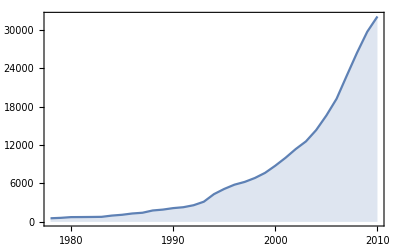

```mathematica
DateListPlot[data⟦All,2⟧,{{1978,1,1},Automatic ,"Year"},Joined->True,Filling->Axis]
```

## 经典模型 - 人口增长logistic模型

### 对于这样一个建立好的模型, 我们只需要丢进数据进行最小二乘拟合出需要的参数即可.

```mathematica
Clear[K,Subscript[N, 0],r,t];
fit = FindFit[data⟦All,2⟧,(K Subscript[N, 0])/(Subscript[N, 0]+(K-Subscript[N, 0]) ⅇ^(-r t)),{K,Subscript[N, 0],r},t]
```

Clear::ssym: N_0 is not a symbol or a string.

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{K→699422.,N_0→391.944,r→0.135775}

```mathematica
model=(K Subscript[N, 0])/(Subscript[N, 0]+(K-Subscript[N, 0]) ⅇ^(-r t))/.fit
```

(2.74135×10^8)/(391.944+699030. ⅇ^(-0.135775 t))

```mathematica
nonlm=NonlinearModelFit[data⟦All,2⟧,(K Subscript[N, 0])/(Subscript[N, 0]+(K-Subscript[N, 0]) ⅇ^(-r t)),{K,Subscript[N, 0],r},t]
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

FittedModel[(2.74135×10^8)/(391.944+699030. ⅇ^(«1»))]

```mathematica
nonlm["Properties"]//Short
```

{AdjustedRSquared,AIC,«46»,StandardizedResiduals,StudentizedResiduals}

```mathematica
nonlm["BestFitParameters"]
```

{K→699422.,N_0→391.944,r→0.135775}

```mathematica
nonlm["FitResiduals"]
```

{117.094,117.86,156.155,80.6054,-3.35947,-95.5371,-27.9837,-50.0516,-15.4305,-93.1961,40.1364,-74.4501,-133.544,-322.385,-391.953,-277.068,416.493,656.871,672.982,364.357,130.967,-33.9744,-22.2204,-47.7264,-118.899,-565.86,-669.73,-515.911,-323.376,540.052,974.45,713.579,-915.259}

```mathematica
nonlm["ANOVATable"]
```

| DF | SS | MS
Model | 3 | 4.7053×10^9 | 1.56843×10^9
Error | 30 | 5.39254×10^6 | 179751.
Uncorrected Total | 33 | 4.71069×10^9 | 
Corrected Total | 32 | 2.61573×10^9 |

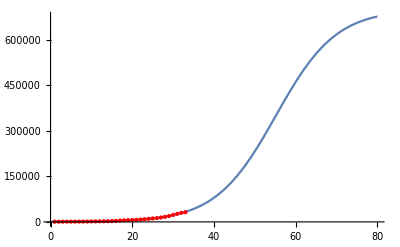

```mathematica
Plot[nonlm["BestFit"],{t,0,80},Epilog->{Red,PointSize[Medium],Point[{Range[Length[data]],data⟦All,2⟧}ᵀ]}]
```

数据类型题目 - 插值

### 直接使用Interpolation函数, 而在Matlab, 你需要根据数据为几维, 是否为网格数据, 选择去用interp1, interp2, griddata(V4), csapi(三次样条), spapi(B样条)等等一大堆......其接口也不是很一致.

```mathematica
X=Table[20*i,{i,0,5}];
Y=Table[40*i,{i,0,5}];
Z={{8.73,8.32,8.00,7.97,7.77,7.99},
     {8.94,8.78,6.87,7.22,7.92,7.99},
    {8.88,8.91,4.21,6.38,7.37,7.95},
     {8.79,8.79,8.54,5.82,4.88,7.97},
     {8.75,8.80,7.91,5.80,4.77,7.85},
     {8.52,8.31,6.61,6.06,6.49,7.97}
    };
```

InterpolatingFunction[{{0., 100.}, {0., 200.}}, <>]

-Graphics3D-

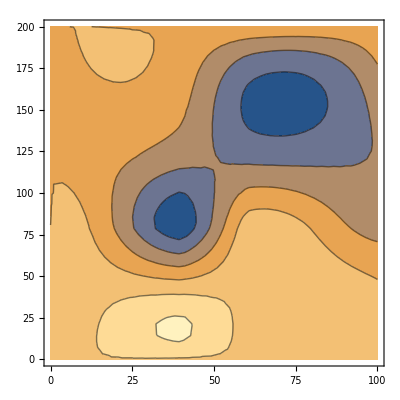

```mathematica
data=Table[{X[[i]],Y[[j]],Z[[i,j]]},{i,6},{j,6}];
data=Flatten[data,1];
f=Interpolation[data]
Show[Plot3D[f[x,y],{x,0,100},{y,0,200}],ListPointPlot3D[data,PlotStyle->Red]]
ContourPlot[f[x,y],{x,0,100},{y,0,200}]
```

数据类型题目 - 预测问题

"LinearRegreesion" | "线性回归"
"NearestNeighbors" | "最近邻方法"
"RandomForest" | "随机森林"
"NeuralNetwork" | "神经网络"

### 常用的预测算法在Mathematica内部都有集成, 我们直接调用Predict函数, 它会为你选出最适合的算法. 说下神经网络, 很多人喜欢用, 原因如下. 1. 容易忽悠. 贴上图片, 一堆介绍, BP算法, 很唬人. 2. 不需要解释结果怎么来的, 因为你也不知道怎么来的(会忽悠点的可以说是自适应学习出来的). 一般来说, 不要把神经网络作为主要的算法, 因为解释性太弱, 可以夹杂在你的模型里, 但是不要作为主体.

## 葡萄酒品质打分预测

### 这里直接调用Mathematica自带的葡萄酒数据集. 这个葡萄酒的数据集包含 3600 组训练集, 和 1200 多组的测试集合, 11 个属性是葡萄酒的11 种化学成分. 通过化学分析可以来推断葡萄酒的质量 (1 ~ 10).

```mathematica
trainingset=ExampleData[{"MachineLearning","WineQuality"},"TrainingData"];
```

```mathematica
trainingset⟦;;3⟧
```

{{7.,0.27,0.36,20.7,0.045,45.,170.,1.001,3.,0.45,8.8}→6.,{6.3,0.3,0.34,1.6,0.049,14.,132.,0.994,3.3,0.49,9.5}→6.,{8.1,0.28,0.4,6.9,0.05,30.,97.,0.9951,3.26,0.44,10.1}→6.}

```mathematica
ExampleData[{"MachineLearning","WineQuality"},"VariableDescriptions"]
```

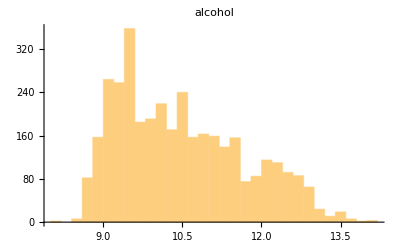
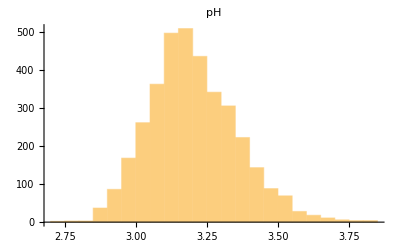

```mathematica
{Histogram[trainingset[[All,1,11]], PlotLabel-> "alcohol"],Histogram[trainingset[[All,1,9]], PlotLabel-> "pH"]}
```

```mathematica
p=Predict[trainingset]
```

PredictorFunction[…]

```mathematica
unknownwine = {7.6,0.48,0.31,9.4,0.046,6.,194.,0.99714,3.07,0.61,9.4};
p[unknownwine]
```

5.4

```mathematica
quality[pH_,alcohol_]:=p[{7.6,0.48,0.31,9.4,0.046,6.,194.,0.99714,pH,0.61,alcohol}];
```

```mathematica
Show[g3=Plot3D[quality[pH,alcohol],{pH,2.8,3.8},{alcohol,8,14},AxesLabel->Automatic],ListPointPlot3D[{{3.07,9.4,p[unknownwine]}},PlotStyle->{Red,PointSize[.05]}]]
```

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value ({7.6,0.48,0.31,9.4,0.046,6.,194.,0.99714,pH,0.61,alcohol}).

-Graphics3D-

## 微分方程

lorenz方程

## Lorenz方程

```mathematica
NDSolve[{x'[t]==-10 (x[t]-y[t]),y'[t]==-x[t] z[t]+28 x[t]-y[t],z'[t]==x[t] y[t]-8/3*z[t],x[0]==5,z[0]==17,y[0]==13},{x,y,z},{t,0,200},MaxSteps->Infinity];
```

```mathematica
Animate[ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.%],{t,0,umax},PlotPoints->10000,ColorFunction->(ColorData["Rainbow"][#4]&),Boxed->False,Axes->False],{umax,0.1,50},AnimationRate->1.2]
```

## 优化问题 函数 | 求解 | 算法 "FindMaximum, FindMinimum" | 数值局部最优化 | 线性规划方法、非线性内点算法、利用二阶导数 "NMaximize, NMinimize" | 数值全局最优化 | 线性规划方法、Nelder-Mead、差分进化、模拟退火、随机搜索 "Maximize, Minimize" | 精确全局最优化 | 线性规划方法、柱形代数分解、拉格朗日乘子法和其他分析方法、整数线性规划 "LinearProgramming" | 线性最优化 | 线性规划方法(单纯型法、修正单纯型法、内点法)

## 优化问题

常见的问题很难找到全局最优解(一般我们只关注足够好的解, 即近似解, 所以就有了玄学智能算法, 这里不讲智能算法的具体细节, 实际上能掌握1-2种就够用了, 所有智能算法都是随机性的算法, 只是随机的策略不同). 除非你从理论上证明这是个凸优化问题, 千万不要自信的说自己找到了全局最优解....

具体到求解的时候, 最好能找到一个好的初始解给算法(自己从题目的理解提供一个好的初始解), 能很大程度的改善计算时间和计算结果.

下面举个例子看看起始点对算法的结果的影响.

## 优化问题

```mathematica
Manipulate[
Module[{min,pts,init},
{min,pts}=Reap[
Quiet[
FindMinimum[f,{{x,r⟦1⟧},{y,r⟦2⟧}},Method->mm,StepMonitor:>If[Norm[{f,x,y}]<10000,Sow[{x,y,f+0.001}]]]
]
];

init=Append[r,f+0.001/.{x->r⟦1⟧,y->r⟦2⟧}];

Show[
Plot3D[f,{x,-5,5},{y,-5,5},
Mesh->30,
MeshFunctions->{#3&},
MeshStyle->GrayLevel[0.6],
PlotLabel->If[Length[pts]==0,Style["No minimum was found.","Label"],Row[{Style["初始点",Green,13,"Label",FontFamily->"微软雅黑"],Style["中间点 points",Darker[Yellow],13,"Label",FontFamily->"微软雅黑"],Style["极值点",Red,13,"Label",FontFamily->"微软雅黑"],Style[Row[{Length[pts⟦1⟧]," 迭代"}],"Label",13,FontFamily->"微软雅黑"]},Spacer[40]]],
PlotStyle->Opacity[.5],
PlotRangePadding->0,
Axes->None,
PlotTheme->"Frame"
],

Graphics3D[
If[Length[pts]==0,
{},
{
{PointSize[.02],Red,Point[Last[Last[pts]]],Green,Point[init],PointSize[.01],Darker[Yellow],Point[pts]},
Thickness[Medium],
Line[Insert[pts,init,{1,1}]]
}
]
],
ImageSize->500,Background-> White
]
],
Style["求函数最小值",15,FontFamily->"微软雅黑"],
Delimiter,"","",
{{r,{-2.5,5},"初始点位置"},{-5,-5},{5,5},ImageSize->Small},
Delimiter,"","",
{{f,(-1/(5+(x-2)^2+(y-2)^2)-1/(4+(x+3)^2+(y+3)^2)),"函数"},{(1-x)^2+100 (y-x^2)^2->"山谷型函数",(x^2/2-0.065625 x^4+x^6/384-(x y)/2+y^2)->"碗型函数",(-1/(5+(x-2)^2+(y-2)^2)-1/(4+(x+3)^2+(y+3)^2))->"双井函数"}
},
Delimiter,"","",
{{mm,Automatic,"最优化算法"},{Automatic->"自动选取","Gradient"->"Gradient","ConjugateGradient"->"Conjugate Gradient","PrincipalAxis"->"Principal Axis","LevenbergMarquardt"->"Levenberg Marquardt","Newton"->"Newton","QuasiNewton"->"Quasi Newton","InteriorPoint"->"Interior Point"}},
LabelStyle->14,ControlPlacement->Right,Paneled->False
]
```

## 优化问题

```mathematica
搜索 f(x,y)=ⅇ^(Sin(50 x))+1/4 (x^2+y^2)+Sin(60 ⅇ^y)-Sin(10 (x+y))+Sin(70 Sin x)+Sin(Sin(80 y)) 的全局极值
```

### 这个函数经常被用来测试一个优化算法的性能, 因为它的形状非常奇葩....我们看看它长什么样

```mathematica
Plot3D[ⅇ^Sin[50 x]+1/4 (x^2+y^2)+Sin[60 ⅇ^y]-Sin[10 (x+y)]+Sin[70 Sin[x]]+Sin[Sin[80 y]],{x,-1,1},{y,-1,1}]
```

-Graphics3D-

```mathematica
NMinimize[ⅇ^Sin[50 x]+1/4 (x^2+y^2)+Sin[60 ⅇ^y]-Sin[10 (x+y)]+Sin[70 Sin[x]]+Sin[Sin[80 y]],{x,y},Method->{"RandomSearch"}]
```

{-2.38708,{x→-0.124868,y→0.290932}}

```mathematica
NMinimize[ⅇ^Sin[50 x]+1/4 (x^2+y^2)+Sin[60 ⅇ^y]-Sin[10 (x+y)]+Sin[70 Sin[x]]+Sin[Sin[80 y]],{x,y},Method->{"RandomSearch","SearchPoints"->1000}]
```

{-3.20814,{x→-0.394526,y→-0.0932002}}

```mathematica
NMinimize[ⅇ^Sin[50 x]+1/4 (x^2+y^2)+Sin[60 ⅇ^y]-Sin[10 (x+y)]+Sin[70 Sin[x]]+Sin[Sin[80 y]],{x,y},Method->{"SimulatedAnnealing","PerturbationScale"->9,"BoltzmannExponent"->Function[{i,df,f0},-df/(Exp[i/10])]}]
```

{-2.90519,{x→-0.394532,y→-0.721187}}

```mathematica
Show[Plot3D[{ⅇ^Sin[50 x]+1/4 (x^2+y^2)+Sin[60 ⅇ^y]-Sin[10 (x+y)]+Sin[70 Sin[x]]+Sin[Sin[80 y]],First@%},{x,-0.5,0.5},{y,-0.5,0.5},PlotStyle->{Opacity[0.6],Automatic},ImageSize-> 400],
Graphics3D[{Red,PointSize[Large] ,Point[-{0.0231,0.4942,3.14}]},ImageSize->250]]
```

-Graphics3D-

## 图论

### 图论应该是属于对算法要求最高的一类, 但是我们一般很少碰到图论题, 当然如果你碰到了, 并且能做出来的话, 拿奖的几率很大. Mathematica在图可视化和图算法可用性方面可以说是最强的(当然这里不讨论符号运算).

最短路

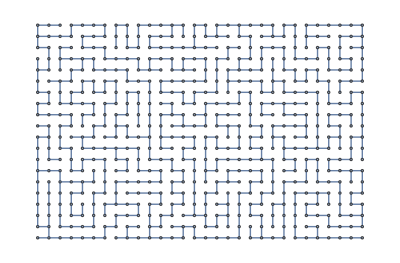

```mathematica
m=-Graphics-
```

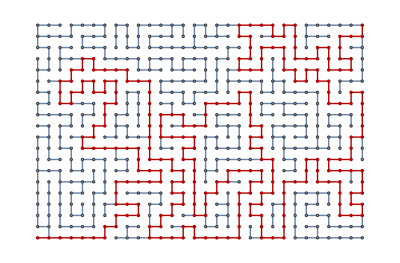

```mathematica
HighlightGraph[m,PathGraph[FindShortestPath[m,First@VertexList[m],Last@VertexList[m]]
]
]
```

最大流

```mathematica
g=-Graphics-
```

-Graphics-

```mathematica
ℱ=FindMaximumFlow[g,"Vancouver","Winnipeg","OptimumFlowData"];
ℱ["FlowValue"]
```

23

```mathematica
Grid[{#,ℱ[#]}&/@ℱ["EdgeList"],Frame-> All,Alignment-> Left]
```

Vancouver->Calgary | 7
Vancouver->Edmonton | 16
Calgary->Regina | 11
Edmonton->Calgary | 4
Edmonton->Saskatoon | 12
Regina->Saskatoon | 7
Regina->Winnipeg | 4
Saskatoon->Winnipeg | 19

```mathematica
Panel[Show[{CountryData["Canada","Shape"],ℱ["FlowGraph"]}, PlotRange->{{-0.31,0.083},{0.04,0.25}}]]
```

-Graphics-

最小生成树

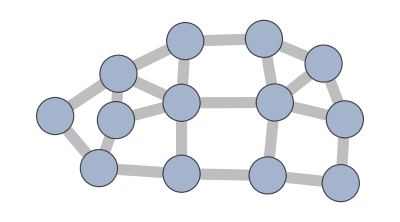

```mathematica
g = Graph[{1<->2,1<->4,2<->3,2<->5,3<->6,4<->5,4<->7,5<->6,5<->8,6<->9,7<->8,7<->10,8<->9,8<->11,9<->12,10<->11,11<->12,12<->13,10<->13,3<->5,8<->12},VertexSize->{0.8},EdgeStyle->{Directive[-Graphics-,Thickness[0.02]]}]
```

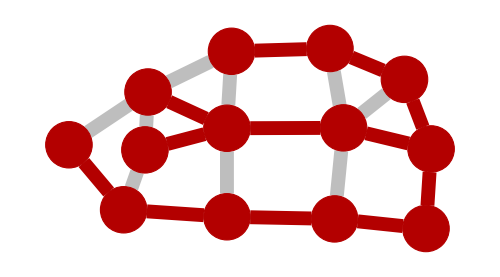

```mathematica
cablenetwork = FindSpanningTree[g];
HighlightGraph[g, cablenetwork, ImageSize -> 500]
```

TSP

### TSP应该是最常见的一类题目, 很多题目都可以转换成TSP问题进行求解, 在Matlab里我们一般用智能算法解. 而在Mathematica里我们只需要一行代码.

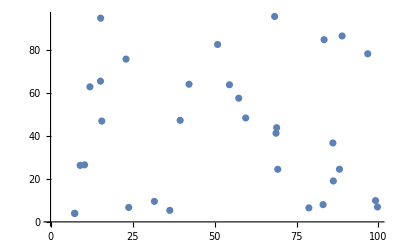

```mathematica
pts=RandomReal[100,{31,2}]/.{a_,b__}:> {a,b,a};
ListPlot[pts]
```

```mathematica
FindShortestTour[pts]
```

{463.375,{1,32,15,2,30,20,11,14,27,4,13,19,16,18,12,6,22,9,28,10,24,17,8,5,3,29,21,31,23,7,25,26,1}}

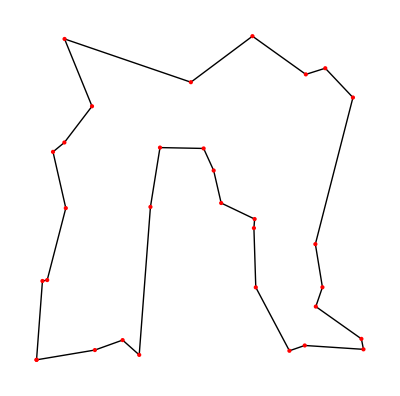

```mathematica
Graphics[{Line[pts⟦Last[FindShortestTour[pts]]⟧],PointSize[Large],Red,Point[pts]}]
```

## 一个好玩的例子 - 用TSP来画图

```mathematica
monalisa=-Graphics-;
```

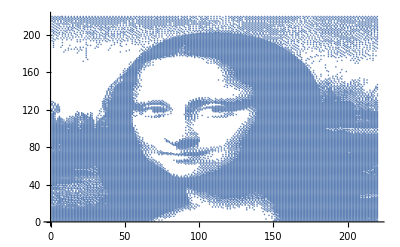

```mathematica
monalisa=ColorQuantize[ColorConvert[monalisa,"Grayscale"],2];
pos=PixelValuePositions[ImageAdjust[monalisa],0];
ListPlot[pos]
```

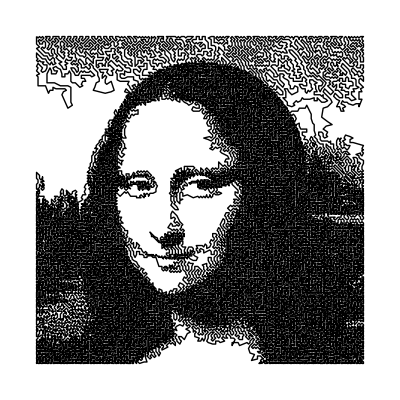

```mathematica
res=FindShortestTour[pos];
Graphics[Line[pos[[res[[2]]]]]]
```

## 资源

帮助文档

官方的资源

```mathematica
demonstrations.wolfram.com 	
		Wolfram Library Archive 和 MathWorld™
```